## Computing Madelung Sums for a Circular Ionic Particle

## The following code is equivalent to summing the inverse distances between two sets of unlike particle positions.

```mathematica
coulombicInteractions[particlePositionsA_, particlePositionsB_]:= 
Total[Total[1.0/ DistanceMatrix[particlePositionsA,particlePositionsB]
]
]
```

#### This is (up to a sign) what needs to be done for the Madelung sums.

This could be done with a double sum over inverse distances, but the above code is clean and efficient.

## The following code is equivalent to summing the inverse distances between a single set of particle distances; that is, over like pairs:

```mathematica
coulombicSelfInteractions[particlePositionsA_]:= Module[

{ numberPositions = Length[particlePositionsA],
augmentedDistanceMatrix },
If[numberPositions ≤ 1, Return[0]];
augmentedDistanceMatrix = DistanceMatrix[particlePositionsA,particlePositionsA] + IdentityMatrix[numberPositions];
(Total[Total[1.0/ augmentedDistanceMatrix ]]- numberPositions)/2

]
```

This could be also done with a double sum over inverse distances, but one has to avoid computing the distance between a particle and itself.  This is what the Identity matrix in the code above is doing.

## An example of using the above code to solve the Madelung sum for a finite dipole chain.

## We will use the recursive method described previously. Its primary advantage is that it is numerically efficient. A secondary advantage is that it is fun to code this way.

### Start by defining the ions to add to the end of a chain. We are doing this in two-dimensions, although that isn’t really necessary.

```mathematica
chainShellAnions[1]= {{}};
chainShellCations[1]= {{}};
chainShellAnions[n_] :={{2n-1,0}}
chainShellCations[n_] := {{ 2n,0}}
```

### Define a chain by adding the shell ions to the existing chain.

```mathematica
chain[1] ={{{1,0}},{{2,0}}}
```

{{{1,0}},{{2,0}}}

#### Our chain is composed of two lists. The first list contains the positions of the anions, and the second (Last) list is for the cations

```mathematica
chain[n_]:= chain[n]= 
{
Join[First[chain[n -1]],chainShellAnions[n]],
Join[Last[chain[n -1]],chainShellCations[n]]
}
```

### Define a chain energy function that takes the energy of a chain of length (n-1) and adds to that the energy of the new interactions. The new interactions have seven parts: 1-4) The interactions between the shell anions/cations with the previous chain’s anions/cations 5) The interactions between the anions in the shell with the other anions in the shell. 6) The interactions between the cations in the shell with the other cations in the shell. 7) The interactions between the cations and anions in the shell.

```mathematica
chainEnergy[1] = -1;
chainEnergy[n_]:=chainEnergy[n]= chainEnergy[n-1] +With[
{previousAnions = chain[n-1][[1]],
previousCations = chain[n-1][[2]]
},
 coulombicInteractions[previousAnions,chainShellAnions[n]]+
 coulombicInteractions[previousCations,chainShellCations[n]] -
coulombicInteractions[previousAnions,chainShellCations[n]]-
 coulombicInteractions[previousCations,chainShellAnions[n]] +
 (
coulombicSelfInteractions[chainShellAnions[n]]+
coulombicSelfInteractions[chainShellCations[n]]
-coulombicInteractions[chainShellCations[n],chainShellAnions[n]]
)
]
```

#### Checking to see how this works:

```mathematica
averageEnergies = Table[{i, chainEnergy[i]/i},{i,1,100}];
```

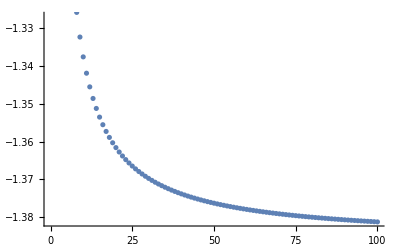

```mathematica
ListPlot[averageEnergies]
```

#### Let’s see if we can fit this curve to get an estimate of the asymptote

```mathematica
model = asymptote + endEnergy/n^p;
```

```mathematica
fit = FindFit[averageEnergies,model,{asymptote,endEnergy,p},n]
```

{asymptote→-1.38948,endEnergy→0.393591,p→0.868178}

```mathematica
model/.fit
```

-1.38948+0.393591/n^0.868178

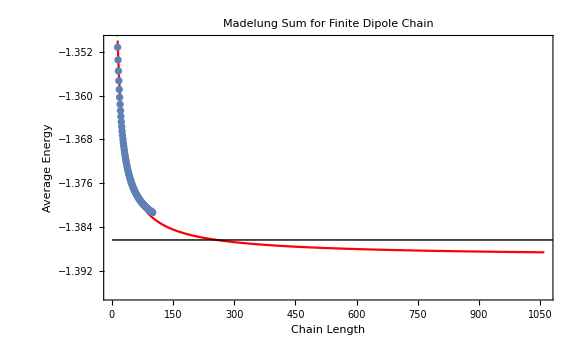

```mathematica
Show[Plot[model/.fit,{n,1,1060},PlotRange->{All, {-2 Log[2]-.01,-1.35}},PlotStyle->Red, Frame->True,
Epilog->Line[{{0,-2 Log[2]},{10^6,-2 Log[2]}}]],ListPlot[averageEnergies],ImageSize->Large,
FrameLabel-> {"Chain Length","Average Energy"},PlotLabel-> "Madelung Sum for Finite Dipole Chain",
BaseStyle->{FontSize->16}]
```

#### The fit is wonky for the first few data points, let’s throw those out to get a better estimate:

```mathematica
fit = FindFit[averageEnergies[[10;;-1]],model,{asymptote,endEnergy,p},n]
```

{asymptote→-1.38645,endEnergy→0.467254,p→0.979682}

```mathematica
model/.fit
```

-1.38645+0.467254/n^0.979682

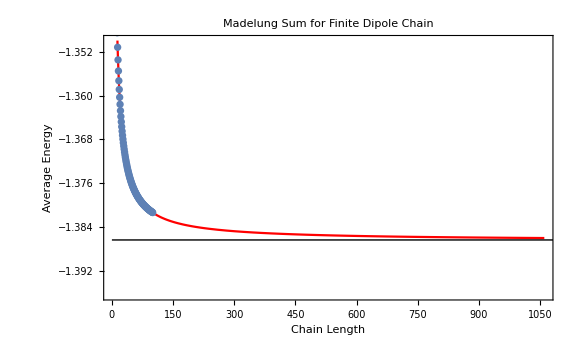

```mathematica
Show[Plot[model/.fit,{n,1,1060},PlotRange->{All, {-2 Log[2]-.01,-1.35}},PlotStyle->Red, Frame->True,
Epilog->Line[{{0,-2 Log[2]},{10^6,-2 Log[2]}}]],ListPlot[averageEnergies],ImageSize->Large,
FrameLabel-> {"Chain Length","Average Energy"},PlotLabel-> "Madelung Sum for Finite Dipole Chain",
BaseStyle->{FontSize->16}]
```

#### Let’s see if the solution gets better by using more points. Here we go up to a chain of length 1000.

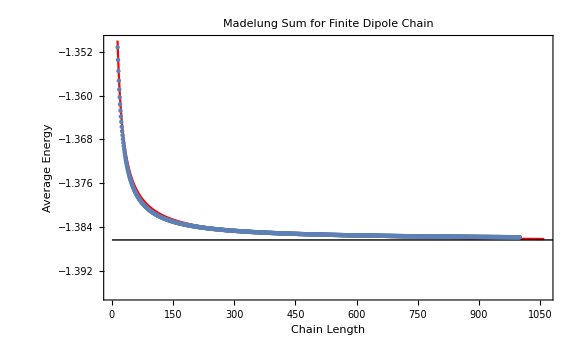

```mathematica
averageEnergies = Table[{i, chainEnergy[i]/i},{i,1,1000}];
fit = FindFit[averageEnergies,model,{asymptote,endEnergy,p},n];
Show[Plot[model/.fit,{n,1,1060},PlotRange->{All, {-2 Log[2]-.01,-1.35}},PlotStyle->Red, Frame->True,
Epilog->Line[{{0,-2 Log[2]},{10^6,-2 Log[2]}}]],ListPlot[averageEnergies],ImageSize->Large,
FrameLabel-> {"Chain Length","Average Energy"},PlotLabel-> "Madelung Sum for Finite Dipole Chain",
BaseStyle->{FontSize->16}]
```

### We’ve demonstrated that the method works well for a known result, now we have confidence that we can generalize to higher dimensions.

## We are going to set this up for a round particle with a square lattice (see Tuples in code below), and with a motif of an anion offset by (-1/4,-1/4) from the lattice points and a cation offset by (1/4,1/4):

```mathematica
Clear[roundParticle,anionShell,cationShell]
```

```mathematica
roundParticle[radius_]:= roundParticle[radius]=
Module[
{
squarePoints = N@Tuples[Range[-radius-2,radius+2],2],
anionOffset = {-1/4,-1/4},
cationOffset = {1/4,1/4},
cationPoints,
anionPoints,
nextAnionShell,
nextCationShell,
innerCationPoints,
innerAnionPoints,
excessCations
},
cationPoints =(# + cationOffset)&/@squarePoints;
anionPoints =(# + anionOffset)&/@squarePoints;
innerCationPoints = Select[cationPoints, Norm[#]≤ radius&];
innerAnionPoints = Select[anionPoints, Norm[#]≤ radius&];
nextCationShell = Select[cationPoints, radius < Norm[#]< radius+1&];
nextAnionShell = Select[anionPoints, radius < Norm[#]< radius+1&];
excessCations = Length[innerCationPoints] + Length[nextCationShell] -
( Length[innerAnionPoints] + Length[nextAnionShell]);
Which[
excessCations>0,
nextCationShell = RandomChoice[nextCationShell,Length[nextCationShell]-excessCations],
excessCations<0,
nextAnionShell = RandomChoice[nextAnionShell,Length[nextAnionShell]-Abs[excessCations]]
];
anionShell[radius+1] = nextAnionShell;
cationShell[radius+1] = nextCationShell;
{innerAnionPoints,innerCationPoints}

]
```

The code above is straightforward conceptually.

1) Make a square lattice

2) Create anion and cation points

3)  Select the anion and cation points within 1 radius of (0,0),  These make up the particle we are after

4) Select the anion and cation points between the  radius  and  (radius+1). These will make up the shell we are after for the next particle.

5) Check for particle charge neutrality and, if necessary, remove some anions or cations from the shell to make the particle neutral .

6) Remember the value of the shells.

7) Return the particle.

#### For example

```mathematica
roundParticle[2]
```

{{{-1.25,-1.25},{-1.25,-0.25},{-1.25,0.75},{-0.25,-1.25},{-0.25,-0.25},{-0.25,0.75},{-0.25,1.75},{0.75,-1.25},{0.75,-0.25},{0.75,0.75},{0.75,1.75},{1.75,-0.25},{1.75,0.75}},{{-1.75,-0.75},{-1.75,0.25},{-0.75,-1.75},{-0.75,-0.75},{-0.75,0.25},{-0.75,1.25},{0.25,-1.75},{0.25,-0.75},{0.25,0.25},{0.25,1.25},{1.25,-0.75},{1.25,0.25},{1.25,1.25}}}

```mathematica
roundParticle[1]
```

{{{-0.25,-0.25},{-0.25,0.75},{0.75,-0.25}},{{-0.75,0.25},{0.25,-0.75},{0.25,0.25}}}

```mathematica
anionShell[2]
```

{{-1.25,-1.25},{-1.25,-0.25},{-1.25,0.75},{-0.25,-1.25},{-0.25,1.75},{0.75,-1.25},{0.75,0.75},{0.75,1.75},{1.75,-0.25},{1.75,0.75}}

#### Illustrating with graphics. Visual debugging is a good practice.

```mathematica
cationGraphic[{x_,y_}]:= {Red,Disk[{x,y},1/5],White,Text["+",{x,y}]}
```

```mathematica
anionGraphic[{x_,y_}]:= {Blue,Disk[{x,y},1/3],White,Text["-",{x,y}]}
```

We will just throw out a few examples

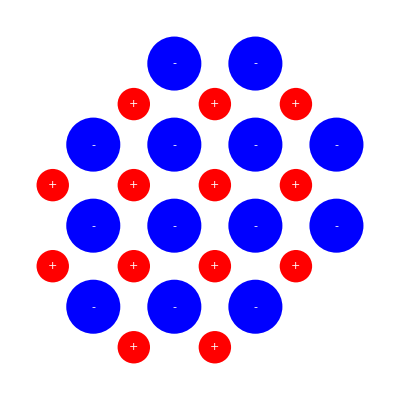

```mathematica
Graphics[
{
anionGraphic[#]&/@roundParticle[2][[1]],
cationGraphic[#]&/@roundParticle[2][[2]]
}
]
```

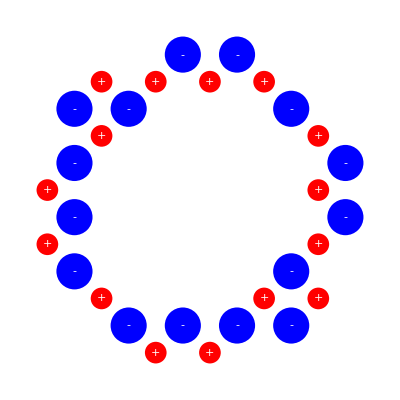

```mathematica
Graphics[
{
anionGraphic[#]&/@anionShell[3],
cationGraphic[#]&/@cationShell[3]
}
]
```

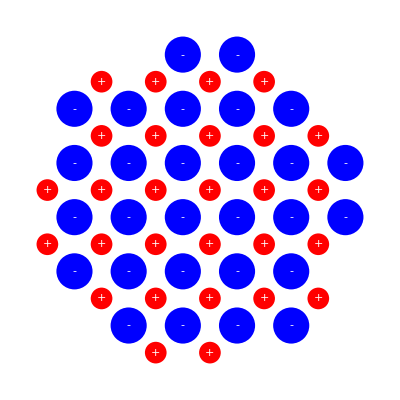

```mathematica
Graphics[
{
anionGraphic[#]&/@roundParticle[2][[1]],
cationGraphic[#]&/@roundParticle[2][[2]],
anionGraphic[#]&/@anionShell[3],
cationGraphic[#]&/@cationShell[3]
}
]
```

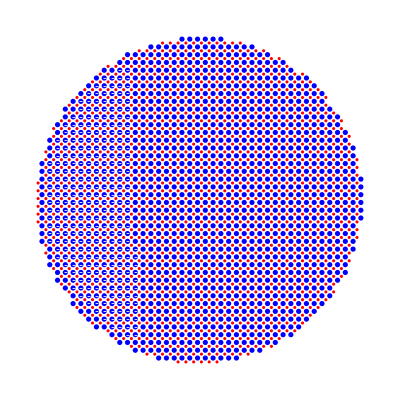

```mathematica
Graphics[
{
anionGraphic[#]&/@roundParticle[20][[1]],
cationGraphic[#]&/@roundParticle[20][[2]],
anionGraphic[#]&/@anionShell[21],
cationGraphic[#]&/@cationShell[21]
}
]
```

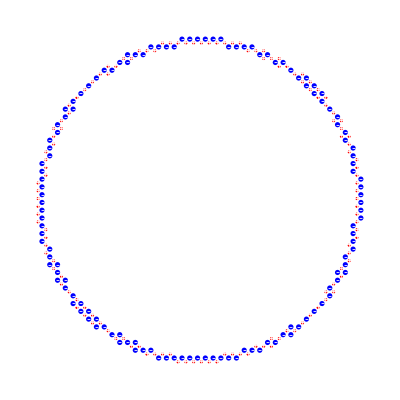

```mathematica
Graphics[
{

anionGraphic[#]&/@anionShell[21],
cationGraphic[#]&/@cationShell[21]
}
]
```

## Now we define our recursive particle energy function, it is nearly identical to the chain example.

```mathematica
Clear[particleEnergy];
particleEnergy[1]= With[
{ 
anions = First[roundParticle[1]],
cations = Last[roundParticle[1]]
},
-coulombicInteractions[anions,cations]+
coulombicSelfInteractions[cations] +
coulombicSelfInteractions[anions]
];


particleEnergy[n_]:=particleEnergy[n]=
 particleEnergy[n-1] +
Module[
{previousAnions = roundParticle[n-1][[1]],
previousCations = roundParticle[n-1][[2]]
},
shellParticle[n]= coulombicInteractions[previousAnions,anionShell[n]]+
 coulombicInteractions[previousCations,cationShell[n]] -
coulombicInteractions[previousAnions,cationShell[n]]-
 coulombicInteractions[previousCations,anionShell[n]];
shellShellLike[n]=coulombicSelfInteractions[anionShell[n]]+
coulombicSelfInteractions[cationShell[n]];
shellUnlike[n]=-coulombicInteractions[cationShell[n],anionShell[n]];
shellParticle[n] + shellShellLike[n] + shellUnlike[n]
]
```

#### Let’s see how it works. We compute the total energy and divide by the number of dipoles for 200 different radii.

```mathematica
averageEnergiesParticle =Table[{i,particleEnergy[i]/(Length[First[roundParticle[i]]])},{i,1,200}];
```

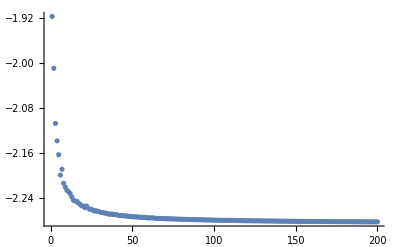

```mathematica
ListPlot[averageEnergiesParticle,PlotRange->All]
```

#### Let’s see if we can find a fit to this curve:

```mathematica
model = asymptote + gamma/(2 Pi r)^p;
```

#### We should expect the power on the radius term to be equal to one.

```mathematica
fit =FindFit[averageEnergiesParticle,model,{asymptote,gamma,p},r]
```

{asymptote→-2.29086,gamma→1.60609,p→0.756702}

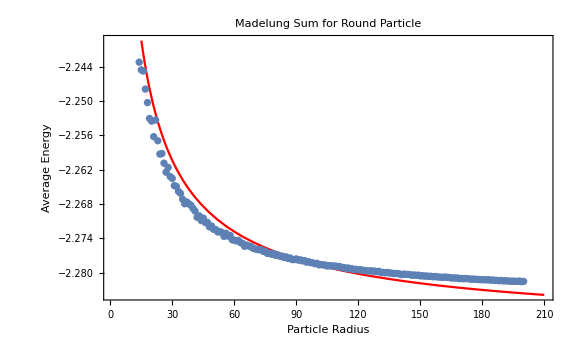

```mathematica
Show[Plot[model/.fit,{r,1,210},PlotStyle->Red, Frame->True]
,ListPlot[averageEnergiesParticle],ImageSize->Large,
FrameLabel-> {"Particle Radius","Average Energy"},PlotLabel-> "Madelung Sum for Round Particle",
BaseStyle->{FontSize->16}]
```

#### Again, the initial points are making the fit wonky, let’s throw out the data for the small radii:

```mathematica
fit =FindFit[averageEnergiesParticle[[10;;-1]],model,{asymptote,gamma,p},r]
```

{asymptote→-2.28494,gamma→3.42437,p→0.971512}

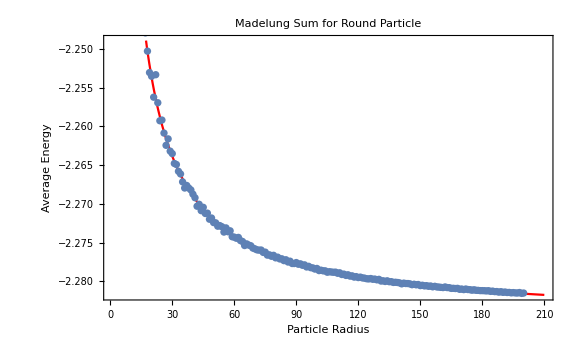

```mathematica
Show[Plot[model/.fit,{r,1,210},PlotStyle->Red, Frame->True]
,ListPlot[averageEnergiesParticle],ImageSize->Large,
FrameLabel-> {"Particle Radius","Average Energy"},PlotLabel-> "Madelung Sum for Round Particle",
BaseStyle->{FontSize->16}]
```

#### Let’s see if there is any benefit to doing a much longer calculation. The following calculation takes a bit over an hour.

```mathematica
averageEnergiesParticle =Table[{i,particleEnergy[i]/(Length[First[roundParticle[i]]])},{i,1,350}];
```

```mathematica
fit =FindFit[averageEnergiesParticle,model,{asymptote,gamma,p},r]
```

{asymptote→-2.28856,gamma→1.6759,p→0.779423}

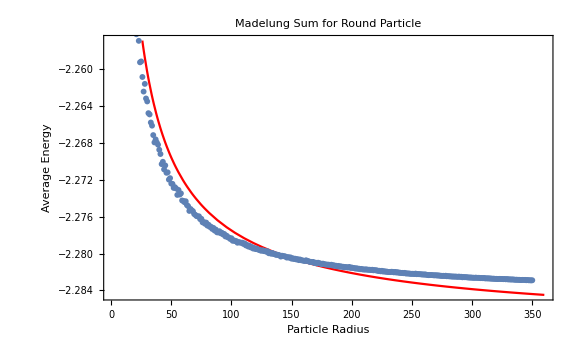

```mathematica
Show[Plot[model/.fit,{r,1,360},PlotStyle->Red, Frame->True]
,ListPlot[averageEnergiesParticle],ImageSize->Large,
FrameLabel-> {"Particle Radius","Average Energy"},PlotLabel-> "Madelung Sum for Round Particle",
BaseStyle->{FontSize->16}]
```

#### Again, the initial points are making the fit wonky, let’s throw out the data for the small radii:

```mathematica
fit =FindFit[averageEnergiesParticle[[10;;-1]],model,{asymptote,gamma,p},r]
```

{asymptote→-2.28484,gamma→3.49999,p→0.976858}

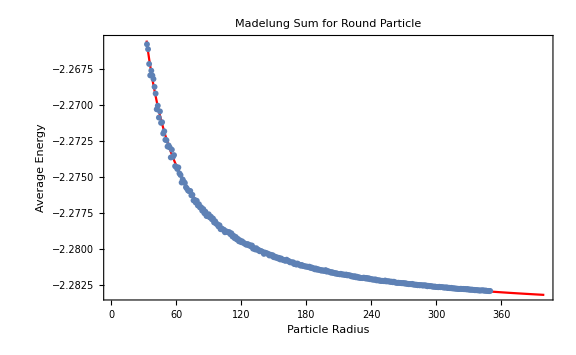

```mathematica
Show[Plot[model/.fit,{r,1,400},PlotStyle->Red, Frame->True]
,ListPlot[averageEnergiesParticle],ImageSize->Large,
FrameLabel-> {"Particle Radius","Average Energy"},PlotLabel-> "Madelung Sum for Round Particle",
BaseStyle->{FontSize->16}]
```

### We conclude that the Madelung Sum for this system is approximately -2.2848 and the surface energy for this configuration is 3.5 (the length unit is the lattice constant).